```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
toplot = {};
qvals=Table[i,{i,2,40}];
nLL=20;
m=1;
V0=3;
L1 =10;
k1s=Table[(2π)/L1 i1,{i1,0,L1-1}];
p=1;
a=1;
g1=2π/a;
```

```mathematica
For[i=1,i<=Length[qvals],i++,
Clear[q,lB,l1,x,H0,Hv,H];
q=qvals[[i]];
lB=a/√(2π p/q);
l1=q/p*a;
x=-1/2 g1^2 lB^2;
k2s=Table[(2π)/a p/q i1/L1,{i1,0,L1-1}];
For[ik1=1,ik1≤Length[k1s],ik1++,
For[ik2=1,ik2≤Length[k2s],ik2++,
k1 =k1s[[ik1]];
k2=k2s[[ik2]];
H0=DiagonalMatrix[Table[1/(m lB^2)(n+1/2),{n,0,nLL}]];
Hv=Table[-4.V0*Cos[k1 l1] √((n!)/(m!))Re[((ⅈ g1 lB)/(√2))^(m-n)Exp[ⅈ g1 k2 lB^2-g1^2 lB^2/4]] LaguerreL[n,m-n,x]UnitStep[m-n],{n,0,nLL},{m,0,nLL}]+
Table[-4.V0*Cos[k1 l1] √((m!)/(n!))Re[((-ⅈ g1 lB)/(√2))^(n-m)Exp[ⅈ g1 k2 lB^2-g1^2 lB^2/4]] LaguerreL[m,n-m,x]UnitStep[n-m-1],{n,0,nLL},{m,0,nLL}];
H = H0 + Hv;
AppendTo[toplot,Thread[{Table[1,{i,0,nLL}]*p/q, Eigenvalues[H]}]]]
];
Print[q]
];
```

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

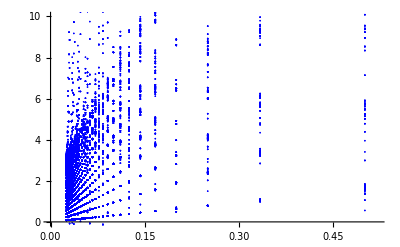

```mathematica
ListPlot[toplot,PlotRange->{{0,0.52},{0,10}},PlotStyle->Blue]
```